# Using Mathematica for Stream Plots of 2D Linear Systems of First-Order ODEs

## Problem Definition

Let’s consider the linear system of differential equations given by 

ẋ=3x - 2y
ẏ=-2x + y
We would like to investigate both the nature of the solutions and the phase plane.  Let’s start by investigating the eigenvalues and eigenvectors.  First, note that we can write the system as 
(ẋ
ẏ) = (3 | -2
-2 | 1)(x
y)
Using this information, we will define a matrix A as follows.  Note that the  A//MatrixForm command simply displays the matrix is a “pretty” format.

```mathematica
A = {{3, -2},{-2,1}};
A//MatrixForm
```

(3 | -2
-2 | 1)

## Determining the Eigenvalues and Eigenvectors

Now that we have defined the matrix A, we can use the command Eigensystem[A] to determine both the eigenvalues and eigenvectors associated with the matrix A.

```mathematica
eigs = Eigensystem[A]
```

{{2+√5,2-√5},{{1/2 (-1-√5),1},{1/2 (-1+√5),1}}}

This output format can be challenging to read.  To get an output that is easier to read, we can simply use the eigs//MatrixForm command to display the output in an easier to read format.

```mathematica
eigs//MatrixForm
```

(2+√5 | 2-√5
{1/2 (-1-√5),1} | {1/2 (-1+√5),1})

Note that we can pick out the separate components of the eigenvalues and eigenvectors.  For example, typing eigs[[1]]  shows us a list of the eigenvalues.  Typing eigs[[2]] shows us a list of the eigenvectors.  We will use these fact later when plotting the eigenvectors.

```mathematica
eigs[[1]]
eigs[[2]]
```

{2+√5,2-√5}

{{1/2 (-1-√5),1},{1/2 (-1+√5),1}}

If we just wanted the first eigenvalue/eigenvector pair, we could type eigs[[1,1]] along with eigs[[2,1]].

```mathematica
eigs[[1,1]]
eigs[[2,1]]
```

2+√5

{1/2 (-1-√5),1}

If we just wanted the individual components of the first eigenvector, we could type eigs[[2,1,1]].

```mathematica
eigs[[2,1,1]]
```

1/2 (-1-√5)

## Creating a plot of the Phase Plane

We can use the StreamPlot to plot the phase plane.  In order to use StreamPlot, we need to create a list in the form {ẋ,ẏ} where ẋ=3x - 2y and ẏ=-2x + y. The easiest way to do this is to create a vector (x
y)  so that we can multiply it by the matrix A.  The following block creates the vector and displays it using the MatrixForm command.

```mathematica
X = {{x},{y}};
X//MatrixForm
```

(x
y)

Note that we can type the command A.x to show the matrix multiplication.  This will generate the list or vector that we will need for the stream plot.

```mathematica
A.X//MatrixForm
```

(3 x-2 y
-2 x+y)

Now, we will create the stream plot by choosing -3 ≤ x,y ≤ 3.  We will also give this some labels and a title.

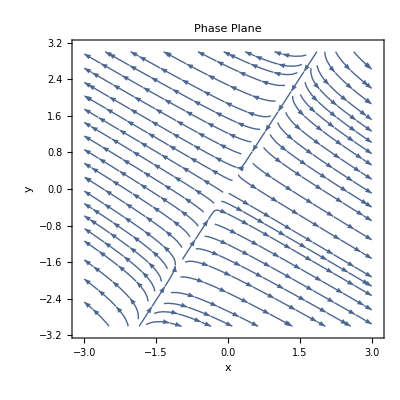

```mathematica
StreamPlot[A.X,{x,-3,3},{y,-3,3},FrameLabel->{"x","y"},PlotLabel->"Phase Plane"]
```

## Plotting the Eigenvectors, Equilibrium Point, and the Phase Plane

Now that we have the phase plane, let’s see how the eigenvectors look on top of this stream plot.  The following block of code creates three separate plots.  Try to make sense of what this command is doing for yourself.  Never simply just copy and paste code.  Always try to understand it for yourself.

P1 is the stream plot.  The same command as above.
P2 is a plot of the eigenvectors.  Here, I’m using a parametric plot but I want to limit the length of each eigenvector to only be plotted within a unit circle (hence the region function).
P3 is simply a plot of the equilibrium point (0,0).  

The final Show command  shows all of the same plots on the same figure.

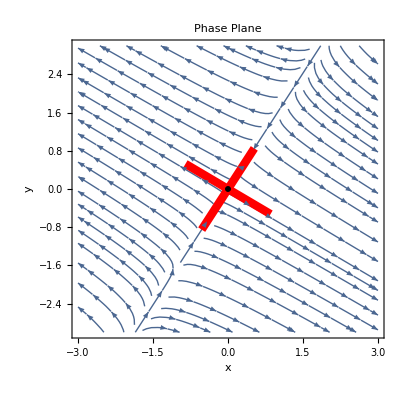

```mathematica
P1 = StreamPlot[A.X,{x,-3,3},{y,-3,3},
FrameLabel->{"x","y"},
PlotLabel->"Phase Plane"];
P2=ParametricPlot[eigs[[2]]*s,{s,-1,1},
PlotStyle->{Red, Thickness->.015},
RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2<1]];
P3 = ListPlot[{{0,0}},
PlotMarkers->{Automatic,Scaled[.04]},
PlotStyle->Black];
Show[P1,P2,P3,PlotRange->All]
```

## Plotting the Solution Curves

Now that we know how the solutions behave in the phase plane, let’s actually solve the differential equation using Mathematica.  We will use the initial conditions x[0] = a, y[0] = b.  We will then plot the solutions for various initial conditions.

```mathematica
ode ={D[x[t],t]==3x[t]-2 y[t],D[y[t],t]==-2 x[t]+y[t]}
iniCond[a_,b_] = {x[0]==a,y[0]== b};
```

{x'[t]==3 x[t]-2 y[t],y'[t]==-2 x[t]+y[t]}

```mathematica
sol[a_,b_] = DSolve[{ode,iniCond[a,b]},{x[t],y[t]},t]//FullSimplify
```

{{x[t]→1/5 ⅇ^(2 t) (5 a Cosh[√5 t]+√5 (a-2 b) Sinh[√5 t]),y[t]→1/5 ⅇ^(2 t) (5 b Cosh[√5 t]-√5 (2 a+b) Sinh[√5 t])}}

Let’s plot the solution for the initial conditions x(0) = 1, y(0) = 1.6.  To do this, we simply plot {x[t],y[t]}/.sol[1,1.6].  Note that I’m also restricting the plot range so that -5 ≤ y ≤ 5.

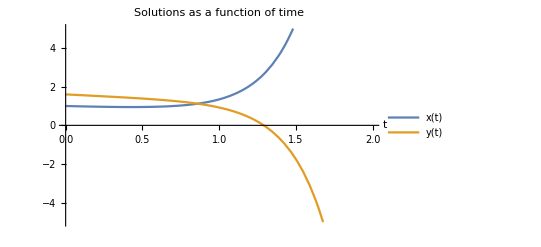

```mathematica
Plot[Evaluate[{x[t],y[t]}/.sol[1,1.6]],{t,0,2},
PlotLabel->"Solutions as a function of time",
AxesLabel->{"t",""},
PlotLegends->{"x(t)","y(t)"},
PlotRange->{-5,5}]
```

Now that we have plotted the function in the time domain (t is our independent variable), let’s plot a parametric representation of the solution in the x-y plane.  Here, we will use the ParametricPlot command again substituting in the initial condition x(0) = 1, y(0) = 1.6.  

Also note that I’m plotting the solution for -2.5 ≤ t ≤ 1.31.  I wanted to plot the solution before the initial time t = 0 to make an interesting comparison with the phase plane later.

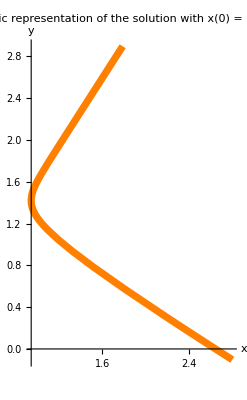

```mathematica
P4 = ParametricPlot[{x[t],y[t]}/.sol[1,1.6],{t,-2.5,1.31},
PlotStyle->{Thickness->0.013,Orange},
AxesLabel->{"x","y"},
PlotLabel->"Parametric representation of the solution with x(0) = 1, y(0) = 1.6"]
```

Now, we can overlay this graph on top of the phase plane plotted earlier.  Note that the parametric representation of the solution matches the what we would expect on given the phase plane.

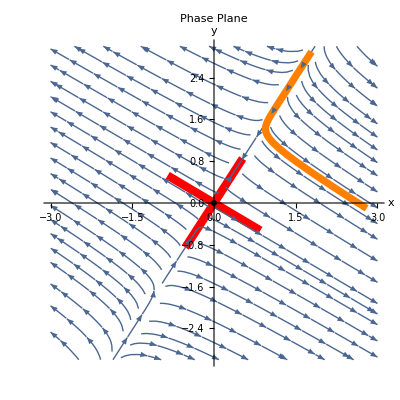

```mathematica
Show[P2,P1,P4,P3,PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Phase Plane"]
```

Ask yourself: what would happen if the initial condition was given as x(0) = -1 +√5,  y(0) = 2? Does your solution make sense?

## One Command to Rule Them All

The following command will work for any linear 2 x 2 system of 1st order ODEs in the form 
ⅆ/ⅆt(x
y)=A(x
y)
where A is a constant 2 x 2 matrix.  This code will:
	* compute and display the `eigensystem`
	* plot the phase plane as in the earlier example

```mathematica
PhasePlane[AA_]:=Module[{XX,esys,Pa,Pb,Pc},
XX = {{x},{y}};
esys = Eigensystem[AA];
Print["For the Matrix A = ",MatrixForm[AA]," the eigenvalues/vectors are",MatrixForm[esys]];
Pa = StreamPlot[AA.X,{x,-3,3},{y,-3,3},FrameLabel->{"x","y"},PlotLabel->"Phase Plane"];
Pb=ParametricPlot[esys[[2]]*s,{s,-1,1},PlotStyle->{Red, Thickness->.015},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2<1]];
Pc = ListPlot[{{0,0}},PlotMarkers->{Automatic,Scaled[.04]},PlotStyle->Black];
Show[Pa,Pb,Pc,PlotRange->All]]
```

Now that we have created a function that will plot the Phase Plane, equilibrium point, and eigenvectors (if real valued), we can call the function for any 2 x 2 constant matrix.  For example, if we want to consider the differential equation  
ⅆ/ⅆt(x
y)=(-1 | 1
-1 | 1)(x
y)
we simply call the command PhasePlane[{{-1,1},{-1,-1}}]

For the Matrix A = (-1 | 1
-1 | -1) the eigenvalues/vectors are(-1+ⅈ | -1-ⅈ
{-ⅈ,1} | {ⅈ,1})

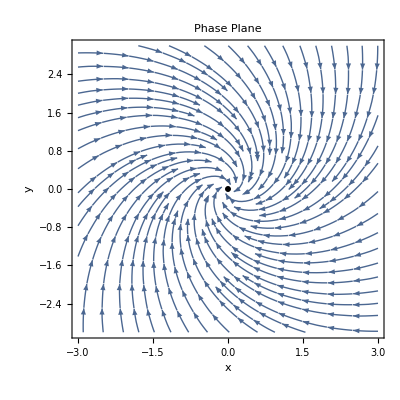

```mathematica
PhasePlane[{{-1,1},{-1,-1}}]
```